```mathematica
filenames={
"Table_Deterministic_TwoHerbicides_control3_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5.txt",
"Table_Deterministic_TwoHerbicides_control1_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5.txt",
"Table_Deterministic_TwoHerbicides_control4_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5.txt",
"Table_Deterministic_TwoHerbicides_control5_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5.txt"};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

```mathematica
data⟦1,All,12⟧//MatrixForm
```

(R1plants
1.55407×10^-6
0.0000435924
0.000760701
0.00854549
0.0759347
0.426968
0.863702
0.977406
0.994581
0.997978
0.999082
0.99956
0.999786
0.999895
0.999948
0.999972
0.999984
0.999991
0.999994
0.999996
0.999997
0.999998
0.999999
0.999999
0.999999
1.
1.
1.
1.
1.)

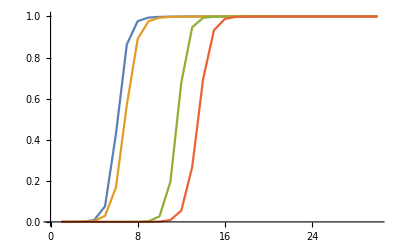

```mathematica
ListPlot[#⟦2;;,12⟧&/@data,Joined->True]
```

## Plot


```mathematica
ListPlot[#⟦2;;,12⟧&/@data,Joined->True,PlotRange->{All,{-0.1,1.1}},Frame->True,PlotMarkers->{{-Graphics-,0.025},{-Graphics-,0.025},{Graphics[{EdgeForm[{Thick,Lighter[Black]}],Lighter[Black],Rectangle[]}],0.025},{Graphics[{EdgeForm[{Thick,Lighter[Black]}],Lighter[Black],Rectangle[]}],0.025},{Graphics[{EdgeForm[Thick],Black,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}],0.025},{Graphics[{EdgeForm[Thick],Black,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}],0.025}},PlotStyle->{Lighter[Gray],Directive[Dashed,Lighter[Gray]],Lighter[Black],Directive[Dashed,Lighter[Black]],Black,Directive[Dashed,Black]},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015],24]]
```